# Числено решаване на обикновени диференциални уравнения

Дадени са следните задачи: (a и b са съответно предпоследната и последната цифра от факултетния номер)
a) y' = y - (2 + a)sinx, y(b) = a + b, x ∈ [b; b + 0.5]
б) y' = y - ln(x^2 + 1) + (2x)/(x^2 + 1) + b, y(a) = a + b, x ∈ [a; a + 0.1]
1. Да се намерят точните решения.
2. Да се решат по методите: Ойлер, модифициран Ойлер, Рунге-Кута (1, 1), Рунге-Кута (2/3, 2/3), Рунге-Кута с 4 междинни точки за а) при h = 0.1, 
за б) при n = 5. Да се направи сравнение между точното решение и численото приближение. Да се представи геометрична интерпретация на резултатите.
3. Колко би трябвало да са n и h за всеки един от посочените методи за всяка от задачите, за да се достигне точност за а) 10^-4, за б) 10^-7?

## Решение на а)

### 1. Да се намерят точните решения

Търсим общо решение:

```mathematica
Clear[x, y]
DSolve[y'[x] ==y[x] - 3Sin[x], y[x], x]
```

{{y[x]→ⅇ^x C[1]+3/2 (Cos[x]+Sin[x])}}

Търсим частно решение:

```mathematica
Clear[x, y]
DSolve[{y'[x] ==y[x] - 3Sin[x], y[9] == 10}, y[x], x]
```

{{y[x]→(20 ⅇ^x-3 ⅇ^x Cos[9]+3 ⅇ^9 Cos[x]-3 ⅇ^x Sin[9]+3 ⅇ^9 Sin[x])/(2 ⅇ^9)}}

Визуализация на точното решение

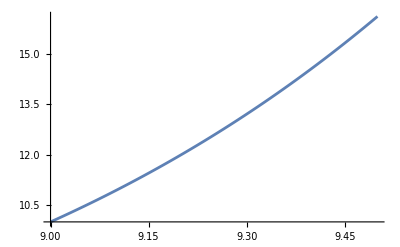

```mathematica
yt[x_] := (20 ⅇ^x-3 ⅇ^x Cos[9]+3 ⅇ^9 Cos[x]-3 ⅇ^x Sin[9]+3 ⅇ^9 Sin[x])/(2 ⅇ^9)
Plot[yt[x], {x, 9,9.5}]
```

Извод: Не можем да намерим точно решение с аналитичен метод

### 2. Да се реши по методите: Ойлер, модифициран Ойлер, Рунге-Кута (1, 1), Рунге-Кута (2/3, 2/3), Рунге-Кута с 4 междинни точки при h = 0.1:

#### 2.1. Ойлер

Мрежата е с n = 5. и стъпка h = 0.1

Теоретичната локална грешка  е 0.01

Теоретичната глобална грешка е 0.1

i = 0 x_i = 9. y_i = 10. f_i = 8.76364 y_точно = 10. Истинска грешка = 0.

i = 1 x_i = 9.1 y_i = 10.8764 f_i = 9.91907 y_точно = 10.936 Истинска грешка = 0.0596498

i = 2 x_i = 9.2 y_i = 11.8683 f_i = 11.1996 y_точно = 12.0003 Истинска грешка = 0.132067

i = 3 x_i = 9.3 y_i = 12.9882 f_i = 12.6149 y_точно = 13.2073 Истинска грешка = 0.219093

i = 4 x_i = 9.4 y_i = 14.2497 f_i = 14.1754 y_точно = 14.5725 Истинска грешка = 0.322809

i = 5 x_i = 9.5 y_i = 15.6673 f_i = 15.8927 y_точно = 16.1128 Истинска грешка = 0.445567

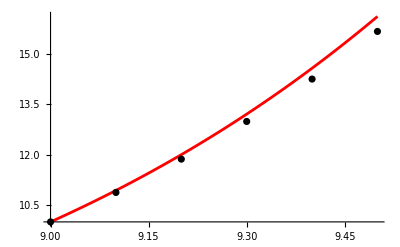

```mathematica
(*Въвеждаме услонието на задачата*)
a = 9.;b=9.5;
x = a;
y =10.;
points = {{x,y}};
f[x_,y_] := y - 3Sin[x]
(*Точно решение*)
yt[x_] := (20 ⅇ^x-3 ⅇ^x Cos[9]+3 ⅇ^9 Cos[x]-3 ⅇ^x Sin[9]+3 ⅇ^9 Sin[x])/(2 ⅇ^9)
(*Съставяме мрежата*)
h = 0.1; n = (b - a)/h;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^2]
Print["Теоретичната глобална грешка е ", h]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y] , " y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y + h*f[x,y];
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

#### 2.2. Модифициран метод на Ойлер

Мрежата е с n = 5. и стъпка h = 0.1

Теоретичната локална грешка  е 0.001

Теоретичната глобална грешка е 0.01

i = 0 x_i = 9. y_i = 10. f_i = 8.76364 x_(i + 1/2) = 9.05 y_(i + 1/2) = 10.4382 f_(i + 1/2) = 9.33998  y_точно = 10. Истинска грешка = 0.

i = 1 x_i = 9.1 y_i = 10.934 f_i = 9.9767 x_(i + 1/2) = 9.15 y_(i + 1/2) = 11.4328 f_(i + 1/2) = 10.6188  y_точно = 10.936 Истинска грешка = 0.00201583

i = 2 x_i = 9.2 y_i = 11.9959 f_i = 11.3272 x_(i + 1/2) = 9.25 y_(i + 1/2) = 12.5622 f_(i + 1/2) = 12.0406  y_точно = 12.0003 Истинска грешка = 0.00445672

i = 3 x_i = 9.3 y_i = 13.1999 f_i = 12.8266 x_(i + 1/2) = 9.35 y_(i + 1/2) = 13.8413 f_(i + 1/2) = 13.6171  y_точно = 13.2073 Истинска грешка = 0.00738565

i = 4 x_i = 9.4 y_i = 14.5617 f_i = 14.4873 x_(i + 1/2) = 9.45 y_(i + 1/2) = 15.286 f_(i + 1/2) = 15.3617  y_точно = 14.5725 Истинска грешка = 0.0108741

i = 5 x_i = 9.5 y_i = 16.0978 f_i = 16.3233 x_(i + 1/2) = 9.55 y_(i + 1/2) = 16.914 f_(i + 1/2) = 17.2887  y_точно = 16.1128 Истинска грешка = 0.0150034

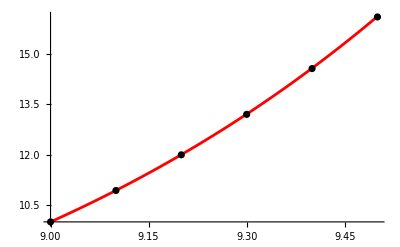

```mathematica
(*Въвеждаме услонието на задачата*)
a = 9.;b=9.5;
x = a;
y =10.;
points = {{x,y}};
f[x_,y_] := y - 3Sin[x]
(*Точно решение*)
yt[x_] := (20 ⅇ^x-3 ⅇ^x Cos[9]+3 ⅇ^9 Cos[x]-3 ⅇ^x Sin[9]+3 ⅇ^9 Sin[x])/(2 ⅇ^9)
(*Съставяме мрежата*)
h = 0.1; n = (b - a)/h;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
x12 = x + h/2;
y12 = y + h/2 f[x,y];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " x_(i + 1/2) = ", x12, " y_(i + 1/2) = ", y12, " f_(i + 1/2) = ", f[x12,y12]  " y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y + h*f[x12,y12];
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle-> Black];
Show[gryt, grp]
```

#### 2.3. РК32 - Формула (1, 1)

Мрежата е с n = 5. и стъпка h = 0.1

Теоретичната локална грешка  е 0.001

Теоретичната глобална грешка е 0.01

i = 0 x_i = 9. y_i = 10. f_i = 8.76364 k_1 = 0.876364 k_2 = 0.991907 y_точно = 10. Истинска грешка = 0.

i = 1 x_i = 9.1 y_i = 10.9341 f_i = 9.97684 k_1 = 0.997684 k_2 = 1.12632 y_точно = 10.936 Истинска грешка = 0.00187858

i = 2 x_i = 9.2 y_i = 11.9961 f_i = 11.3275 k_1 = 1.13275 k_2 = 1.27555 y_точно = 12.0003 Истинска грешка = 0.00420333

i = 3 x_i = 9.3 y_i = 13.2003 f_i = 12.8269 k_1 = 1.28269 k_2 = 1.44087 y_точно = 13.2073 Истинска грешка = 0.00704046

i = 4 x_i = 9.4 y_i = 14.5621 f_i = 14.4877 k_1 = 1.44877 k_2 = 1.62363 y_точно = 14.5725 Истинска грешка = 0.0104647

i = 5 x_i = 9.5 y_i = 16.0983 f_i = 16.3237 k_1 = 1.63237 k_2 = 1.82536 y_точно = 16.1128 Истинска грешка = 0.0145605

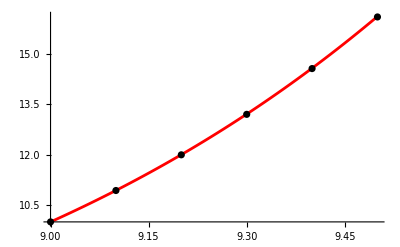

```mathematica
(*Въвеждаме услонието на задачата*)
a = 9.;b=9.5;
x = a;
y =10.;
points = {{x,y}};
f[x_,y_] := y - 3Sin[x]
(*Точно решение*)
yt[x_] := (20 ⅇ^x-3 ⅇ^x Cos[9]+3 ⅇ^9 Cos[x]-3 ⅇ^x Sin[9]+3 ⅇ^9 Sin[x])/(2 ⅇ^9)
(*Съставяме мрежата*)
h = 0.1; n = (b - a)/h;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
k1 = h *  f[x,y];
k2 = h *  f[x + h,y + k1];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " k_1 = ", k1, " k_2 = ", k2," y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y + 1/2(k1+k2);
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

#### 2.4. РК32 - Формула (2/3, 2/3)

Мрежата е с n = 5. и стъпка h = 0.1

Теоретичната локална грешка  е 0.001

Теоретичната глобална грешка е 0.01

i = 0 x_i = 9. y_i = 10. f_i = 8.76364 k_1 = 0.876364 k_2 = 0.953273 y_точно = 10. Истинска грешка = 0.

i = 1 x_i = 9.1 y_i = 10.934 f_i = 9.97675 k_1 = 0.997675 k_2 = 1.08334 y_точно = 10.936 Истинска грешка = 0.00196878

i = 2 x_i = 9.2 y_i = 11.996 f_i = 11.3273 k_1 = 1.13273 k_2 = 1.22788 y_точно = 12.0003 Истинска грешка = 0.00436949

i = 3 x_i = 9.3 y_i = 13.2001 f_i = 12.8267 k_1 = 1.28267 k_2 = 1.38809 y_точно = 13.2073 Истинска грешка = 0.00726616

i = 4 x_i = 9.4 y_i = 14.5618 f_i = 14.4875 k_1 = 1.44875 k_2 = 1.56533 y_точно = 14.5725 Истинска грешка = 0.0107314

i = 5 x_i = 9.5 y_i = 16.098 f_i = 16.3234 k_1 = 1.63234 k_2 = 1.76104 y_точно = 16.1128 Истинска грешка = 0.0148474

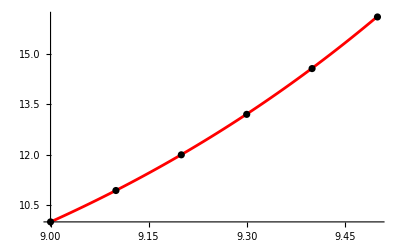

```mathematica
(*Въвеждаме услонието на задачата*)
a = 9.;b=9.5;
x = a;
y =10.;
points = {{x,y}};
f[x_,y_] := y - 3Sin[x]
(*Точно решение*)
yt[x_] := (20 ⅇ^x-3 ⅇ^x Cos[9]+3 ⅇ^9 Cos[x]-3 ⅇ^x Sin[9]+3 ⅇ^9 Sin[x])/(2 ⅇ^9)
(*Съставяме мрежата*)
h = 0.1; n = (b - a)/h;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
k1 = h *  f[x,y];
k2 = h *  f[x + 2/3*h,y + 2/3* k1];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " k_1 = ", k1, " k_2 = ", k2," y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y +1/4*k1 + 3/4 *k2;
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

#### 2.5. РК54 - Формула с четири междинни точки

Мрежата е с n = 5. и стъпка h = 0.1

Теоретичната локална грешка  е 0.00001

Теоретичната глобална грешка е 0.0001

i = 0 x_i = 9. y_i = 10. f_i = 8.76364 k_1 = 0.876364 k_2 = 0.933998 k_3 = 0.93688 k_4 = 0.997959 y_точно = 10. Истинска грешка = 0.

i = 1 x_i = 9.1 y_i = 10.936 f_i = 9.97872 k_1 = 0.997872 k_2 = 1.06209 k_3 = 1.06531 k_4 = 1.13326 y_точно = 10.936 Истинска грешка = 9.16402×10^-7

i = 2 x_i = 9.2 y_i = 12.0003 f_i = 11.3317 k_1 = 1.13317 k_2 = 1.20453 k_3 = 1.20809 k_4 = 1.28351 y_точно = 12.0003 Истинска грешка = 2.04454×10^-6

i = 3 x_i = 9.3 y_i = 13.2073 f_i = 12.834 k_1 = 1.2834 k_2 = 1.36249 k_3 = 1.36644 k_4 = 1.44994 y_точно = 13.2073 Истинска грешка = 3.41652×10^-6

i = 4 x_i = 9.4 y_i = 14.5725 f_i = 14.4982 k_1 = 1.44982 k_2 = 1.53731 k_3 = 1.54168 k_4 = 1.63397 y_точно = 14.5725 Истинска грешка = 5.06867×10^-6

i = 5 x_i = 9.5 y_i = 16.1128 f_i = 16.3383 k_1 = 1.63383 k_2 = 1.73044 k_3 = 1.73527 k_4 = 1.83711 y_точно = 16.1128 Истинска грешка = 7.04212×10^-6

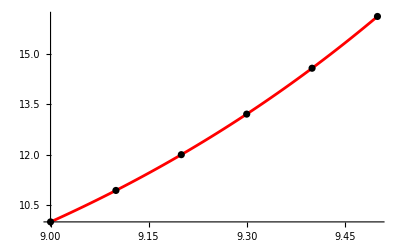

```mathematica
a = 9.;b=9.5;
x = a;
y =10.;
points = {{x,y}};
f[x_,y_] := y - 3Sin[x]
(*Точно решение*)
yt[x_] := (20 ⅇ^x-3 ⅇ^x Cos[9]+3 ⅇ^9 Cos[x]-3 ⅇ^x Sin[9]+3 ⅇ^9 Sin[x])/(2 ⅇ^9)
(*Съставяме мрежата*)
h = 0.1; n = (b - a)/h;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
k1 = h *  f[x,y];
k2 = h *  f[x + h/2,y + k1/2];
k3 = h *  f[x + h/2,y + k2/2];
k4 = h *  f[x + h,y + k3];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " k_1 = ", k1, " k_2 = ", k2, " k_3 = ", k3, " k_4 = ", k4, " y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y +1/6(k1 + 2k2 + 2k3 + k4);
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

### 3. Колко би трябвало да са n и h за всеки един от посочените методи, за да се достигне точност 10^-4

#### 2.1. Ойлер

```mathematica
a = 9.;b=9.5;
Clear[n]
Reduce[(b-a)/n <= 10^-4]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥5000.

```mathematica
(*Въвеждаме услонието на задачата*)
a = 9.;b=9.5;
x = a;
y =10.;
points = {{x,y}};
f[x_,y_] := y - 3Sin[x]
(*Точно решение*)
yt[x_] := (20 ⅇ^x-3 ⅇ^x Cos[9]+3 ⅇ^9 Cos[x]-3 ⅇ^x Sin[9]+3 ⅇ^9 Sin[x])/(2 ⅇ^9)
(*Съставяме мрежата*)
n= 5000; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^2]
Print["Теоретичната глобална грешка е ", h]
```

Мрежата е с n = 5000 и стъпка h = 0.0001

Теоретичната локална грешка  е 1.×10^-8

Теоретичната глобална грешка е 0.0001

#### 2.2. Модифициран метод на Ойлер

```mathematica
a = 9.;b=9.5;
Clear[n]
Reduce[(b-a)/n <= 10^-4]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥5000.

```mathematica
(*Въвеждаме услонието на задачата*)
a = 9.;b=9.5;
x = a;
y =10.;
points = {{x,y}};
f[x_,y_] := y - 3Sin[x]
(*Точно решение*)
yt[x_] := (20 ⅇ^x-3 ⅇ^x Cos[9]+3 ⅇ^9 Cos[x]-3 ⅇ^x Sin[9]+3 ⅇ^9 Sin[x])/(2 ⅇ^9)
(*Съставяме мрежата*)
n= 5000; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
```

Мрежата е с n = 5000 и стъпка h = 0.0001

Теоретичната локална грешка  е 1.×10^-12

Теоретичната глобална грешка е 1.×10^-8

#### 2.3. РК32 - Формула (1, 1)

```mathematica
Clear[n]
Reduce[((b-a)/n)^2 <= 10^-4,n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-50.||n≥50.

```mathematica
(*Въвеждаме услонието на задачата*)
a = 9.;b=9.5;
x = a;
y =10.;
points = {{x,y}};
f[x_,y_] := y - 3Sin[x]
(*Точно решение*)
yt[x_] := (20 ⅇ^x-3 ⅇ^x Cos[9]+3 ⅇ^9 Cos[x]-3 ⅇ^x Sin[9]+3 ⅇ^9 Sin[x])/(2 ⅇ^9)
(*Съставяме мрежата*)
n = 50; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
```

Мрежата е с n = 50 и стъпка h = 0.01

Теоретичната локална грешка  е 1.×10^-6

Теоретичната глобална грешка е 0.0001

#### 2.4. РК32 - Формула (2/3, 2/3)

```mathematica
Clear[n]
Reduce[((b-a)/n)^2 <= 10^-4,n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-50.||n≥50.

```mathematica
(*Въвеждаме услонието на задачата*)
a = 9.;b=9.5;
x = a;
y =10.;
points = {{x,y}};
f[x_,y_] := y - 3Sin[x]
(*Точно решение*)
yt[x_] := (20 ⅇ^x-3 ⅇ^x Cos[9]+3 ⅇ^9 Cos[x]-3 ⅇ^x Sin[9]+3 ⅇ^9 Sin[x])/(2 ⅇ^9)
(*Съставяме мрежата*)
n = 50; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
```

Мрежата е с n = 50 и стъпка h = 0.01

Теоретичната локална грешка  е 1.×10^-6

Теоретичната глобална грешка е 0.0001

#### 2.5. РК54 - Формула с четири междинни точки

```mathematica
Clear[n]
Reduce[((b-a)/n)^4 <= 10^-4, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-5.||n≥5.

```mathematica
a = 9.;b=9.5;
x = a;
y =10.;
points = {{x,y}};
f[x_,y_] := y - 3Sin[x]
(*Точно решение*)
yt[x_] := (20 ⅇ^x-3 ⅇ^x Cos[9]+3 ⅇ^9 Cos[x]-3 ⅇ^x Sin[9]+3 ⅇ^9 Sin[x])/(2 ⅇ^9)
(*Съставяме мрежата*)
n = 5; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
```

Мрежата е с n = 5 и стъпка h = 0.1

Теоретичната локална грешка  е 0.00001

Теоретичната глобална грешка е 0.0001

## Решение на б)

### 1. Да се намерят точните решения

Търсим общо решение:

```mathematica
Clear[x, y]
DSolve[y'[x] ==y[x] - Log[x^2 + 1] + (2x)/(x^2 + 1) + 9, y[x], x]
```

{{y[x]→-9+ⅇ^x C[1]+Log[1+x^2]}}

Търсим частно решение:

```mathematica
Clear[x, y]
DSolve[{y'[x] ==y[x] - Log[x^2 + 1] + (2x)/(x^2 + 1) + 9, y[1] == 10}, y[x], x]
```

{{y[x]→(-9 ⅇ+19 ⅇ^x-ⅇ^x Log[2]+ⅇ Log[1+x^2])/ⅇ}}

Визуализация на точното решение

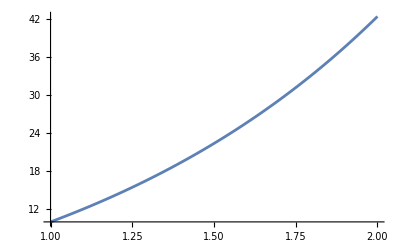

```mathematica
yt[x_] := (-9 ⅇ+19 ⅇ^x-ⅇ^x Log[2]+ⅇ Log[1+x^2])/ⅇ
Plot[yt[x], {x,1,2}]
```

Извод: Не можем да намерим точно решение с аналитичен метод

### 2. Да се реши по методите: Ойлер, модифициран Ойлер, Рунге-Кута (1, 1), Рунге-Кута (2/3, 2/3), Рунге-Кута с 4 междинни точки при n = 5:

#### 2.1. Ойлер

Мрежата е с n = 5 и стъпка h = 0.2

Теоретичната локална грешка  е 0.04

Теоретичната глобална грешка е 0.2

i = 0 x_i = 1. y_i = 10. f_i = 19.3069 y_точно = 10. Истинска грешка = 0.

i = 1 x_i = 1.2 y_i = 13.8614 f_i = 22.953 y_точно = 14.252 Истинска грешка = 0.390668

i = 2 x_i = 1.4 y_i = 18.452 f_i = 27.3127 y_точно = 19.3958 Истинска грешка = 0.943838

i = 3 x_i = 1.6 y_i = 23.9145 f_i = 32.5436 y_точно = 25.627 Истинска грешка = 1.71251

i = 4 x_i = 1.8 y_i = 30.4232 f_i = 38.8277 y_точно = 33.1872 Истинска грешка = 2.76398

i = 5 x_i = 2. y_i = 38.1888 f_i = 46.3793 y_точно = 42.3726 Истинска грешка = 4.18384

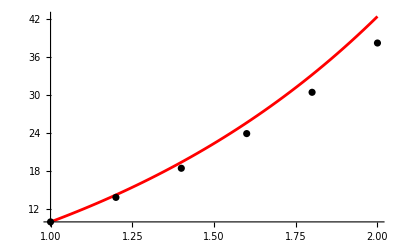

```mathematica
(*Въвеждаме услонието на задачата*)
a = 1.;b=2.;
x = a;
y =10.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 9
(*Точно решение*)
yt[x_] := (-9 ⅇ+19 ⅇ^x-ⅇ^x Log[2]+ⅇ Log[1+x^2])/ⅇ
(*Съставяме мрежата*)
n = 5; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^2]
Print["Теоретичната глобална грешка е ", h]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y] , " y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y + h*f[x,y];
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

#### 2.2. Модифициран метод на Ойлер

Мрежата е с n = 5 и стъпка h = 0.2

Теоретичната локална грешка  е 0.008

Теоретичната глобална грешка е 0.04

i = 0 x_i = 1. y_i = 10. f_i = 19.3069 x_(i + 1/2) = 1.1 y_(i + 1/2) = 11.9307 f_(i + 1/2) = 21.1332  y_точно = 10. Истинска грешка = 0.

i = 1 x_i = 1.2 y_i = 14.2266 f_i = 23.3182 x_(i + 1/2) = 1.3 y_(i + 1/2) = 16.5585 f_(i + 1/2) = 25.5355  y_точно = 14.252 Истинска грешка = 0.025405

i = 2 x_i = 1.4 y_i = 19.3337 f_i = 28.1945 x_(i + 1/2) = 1.5 y_(i + 1/2) = 22.1532 f_(i + 1/2) = 30.8976  y_точно = 19.3958 Истинска грешка = 0.062079

i = 3 x_i = 1.6 y_i = 25.5132 f_i = 34.1424 x_(i + 1/2) = 1.7 y_(i + 1/2) = 28.9275 f_(i + 1/2) = 37.4431  y_точно = 25.627 Истинска грешка = 0.113777

i = 4 x_i = 1.8 y_i = 33.0019 f_i = 41.4064 x_(i + 1/2) = 1.9 y_(i + 1/2) = 37.1425 f_(i + 1/2) = 45.4386  y_точно = 33.1872 Истинска грешка = 0.185347

i = 5 x_i = 2. y_i = 42.0896 f_i = 50.2801 x_(i + 1/2) = 2.1 y_(i + 1/2) = 47.1176 f_(i + 1/2) = 55.2057  y_точно = 42.3726 Истинска грешка = 0.283043

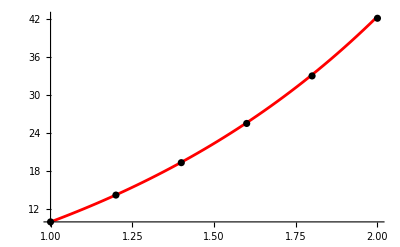

```mathematica
(*Въвеждаме услонието на задачата*)
a = 1.;b=2.;
x = a;
y =10.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 9
(*Точно решение*)
yt[x_] := (-9 ⅇ+19 ⅇ^x-ⅇ^x Log[2]+ⅇ Log[1+x^2])/ⅇ
(*Съставяме мрежата*)
n = 5; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
x12 = x + h/2;
y12 = y + h/2 f[x,y];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " x_(i + 1/2) = ", x12, " y_(i + 1/2) = ", y12, " f_(i + 1/2) = ", f[x12,y12]  " y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y + h*f[x12,y12];
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle-> Black];
Show[gryt, grp]
```

#### 2.3. РК32 - Формула (1, 1)

Мрежата е с n = 5 и стъпка h = 0.2

Теоретичната локална грешка  е 0.008

Теоретичната глобална грешка е 0.04

i = 0 x_i = 1. y_i = 10. f_i = 19.3069 k_1 = 3.86137 k_2 = 4.5906 y_точно = 10. Истинска грешка = 0.

i = 1 x_i = 1.2 y_i = 14.226 f_i = 23.3176 k_1 = 4.66352 k_2 = 5.55005 y_точно = 14.252 Истинска грешка = 0.0260554

i = 2 x_i = 1.4 y_i = 19.3328 f_i = 28.1935 k_1 = 5.6387 k_2 = 6.72012 y_точно = 19.3958 Истинска грешка = 0.0630363

i = 3 x_i = 1.6 y_i = 25.5122 f_i = 34.1413 k_1 = 6.82826 k_2 = 8.14899 y_точно = 25.627 Истинска грешка = 0.114842

i = 4 x_i = 1.8 y_i = 33.0008 f_i = 41.4053 k_1 = 8.28106 k_2 = 9.89448 y_точно = 33.1872 Истинска грешка = 0.186411

i = 5 x_i = 2. y_i = 42.0886 f_i = 50.2791 k_1 = 10.0558 k_2 = 12.0266 y_точно = 42.3726 Истинска грешка = 0.284049

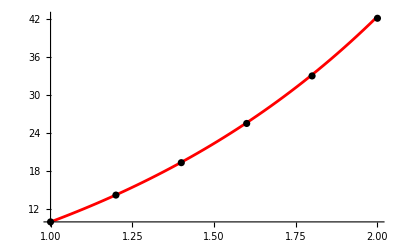

```mathematica
(*Въвеждаме услонието на задачата*)
a = 1.;b=2.;
x = a;
y =10.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 9
(*Точно решение*)
yt[x_] := (-9 ⅇ+19 ⅇ^x-ⅇ^x Log[2]+ⅇ Log[1+x^2])/ⅇ
(*Съставяме мрежата*)
n = 5; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
k1 = h *  f[x,y];
k2 = h *  f[x + h,y + k1];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " k_1 = ", k1, " k_2 = ", k2," y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y + 1/2(k1+k2);
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

#### 2.4. РК32 - Формула (2/3, 2/3)

Мрежата е с n = 5 и стъпка h = 0.2

Теоретичната локална грешка  е 0.008

Теоретичната глобална грешка е 0.04

i = 0 x_i = 1. y_i = 10. f_i = 19.3069 k_1 = 3.86137 k_2 = 4.34807 y_точно = 10. Истинска грешка = 0.

i = 1 x_i = 1.2 y_i = 14.2264 f_i = 23.318 k_1 = 4.6636 k_2 = 5.25476 y_точно = 14.252 Истинска грешка = 0.0256446

i = 2 x_i = 1.4 y_i = 19.3334 f_i = 28.1941 k_1 = 5.63882 k_2 = 6.35968 y_точно = 19.3958 Истинска грешка = 0.0624389

i = 3 x_i = 1.6 y_i = 25.5128 f_i = 34.1419 k_1 = 6.82839 k_2 = 7.70868 y_точно = 25.627 Истинска грешка = 0.114188

i = 4 x_i = 1.8 y_i = 33.0014 f_i = 41.4059 k_1 = 8.28119 k_2 = 9.35656 y_точно = 33.1872 Истинска грешка = 0.185774

i = 5 x_i = 2. y_i = 42.0892 f_i = 50.2797 k_1 = 10.0559 k_2 = 11.3695 y_точно = 42.3726 Истинска грешка = 0.283468

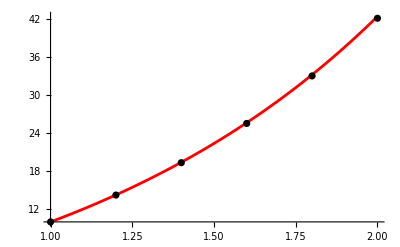

```mathematica
(*Въвеждаме услонието на задачата*)
a = 1.;b=2.;
x = a;
y =10.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 9
(*Точно решение*)
yt[x_] := (-9 ⅇ+19 ⅇ^x-ⅇ^x Log[2]+ⅇ Log[1+x^2])/ⅇ
(*Съставяме мрежата*)
n = 5; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
k1 = h *  f[x,y];
k2 = h *  f[x + 2/3*h,y + 2/3* k1];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " k_1 = ", k1, " k_2 = ", k2," y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y +1/4*k1 + 3/4 *k2;
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

#### 2.5. РК54 - Формула с четири междинни точки

Мрежата е с n = 5 и стъпка h = 0.2

Теоретичната локална грешка  е 0.00032

Теоретичната глобална грешка е 0.0016

i = 0 x_i = 1. y_i = 10. f_i = 19.3069 k_1 = 3.86137 k_2 = 4.22663 k_3 = 4.26316 k_4 = 4.67095 y_точно = 10. Истинска грешка = 0.

i = 1 x_i = 1.2 y_i = 14.252 f_i = 23.3436 k_1 = 4.66872 k_2 = 5.11267 k_3 = 5.15706 k_4 = 5.65396 y_точно = 14.252 Истинска грешка = 0.0000533747

i = 2 x_i = 1.4 y_i = 19.3957 f_i = 28.2564 k_1 = 5.65129 k_2 = 6.19315 k_3 = 6.24733 k_4 = 6.85443 y_точно = 19.3958 Истинска грешка = 0.000128089

i = 3 x_i = 1.6 y_i = 25.6268 f_i = 34.2559 k_1 = 6.85118 k_2 = 7.5136 k_3 = 7.57984 k_4 = 8.32223 y_точно = 25.627 Истинска грешка = 0.000231966

i = 4 x_i = 1.8 y_i = 33.1868 f_i = 41.5913 k_1 = 8.31827 k_2 = 9.12841 k_3 = 9.20942 k_4 = 10.1174 y_точно = 33.1872 Истинска грешка = 0.00037495

i = 5 x_i = 2. y_i = 42.3721 f_i = 50.5626 k_1 = 10.1125 k_2 = 11.1033 k_3 = 11.2024 k_4 = 12.3126 y_точно = 42.3726 Истинска грешка = 0.000569682

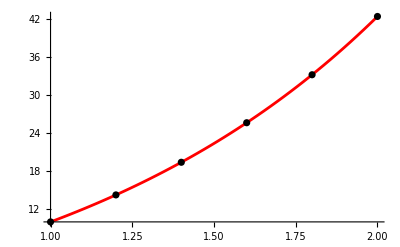

```mathematica
(*Въвеждаме услонието на задачата*)
a = 1.;b=2.;
x = a;
y =10.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 9
(*Точно решение*)
yt[x_] := (-9 ⅇ+19 ⅇ^x-ⅇ^x Log[2]+ⅇ Log[1+x^2])/ⅇ
(*Съставяме мрежата*)
n = 5; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
k1 = h *  f[x,y];
k2 = h *  f[x + h/2,y + k1/2];
k3 = h *  f[x + h/2,y + k2/2];
k4 = h *  f[x + h,y + k3];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " k_1 = ", k1, " k_2 = ", k2, " k_3 = ", k3, " k_4 = ", k4, " y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y +1/6(k1 + 2k2 + 2k3 + k4);
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

### 3. Колко би трябвало да са n и h за всеки един от посочените методи, за да се достигне точност 10^-7

#### 2.1. Ойлер

```mathematica
a = 1.;b=2.;
Clear[n]
Reduce[(b-a)/n <= 10^-7]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥1.×10^7

```mathematica
(*Въвеждаме услонието на задачата*)
a = 1.;b=2.;
x = a;
y =10.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 9
(*Точно решение*)
yt[x_] := (-9 ⅇ+19 ⅇ^x-ⅇ^x Log[2]+ⅇ Log[1+x^2])/ⅇ
(*Съставяме мрежата*)
n = 10^7; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^2]
Print["Теоретичната глобална грешка е ", h]
```

Мрежата е с n = 10000000 и стъпка h = 1.×10^-7

Теоретичната локална грешка  е 1.×10^-14

Теоретичната глобална грешка е 1.×10^-7

#### 2.2. Модифициран метод на Ойлер

```mathematica
a = 1.;b=2.;
Clear[n]
Reduce[(b-a)/n <= 10^-7]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥1.×10^7

```mathematica
(*Въвеждаме услонието на задачата*)
a = 1.;b=2.;
x = a;
y =10.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 9
(*Точно решение*)
yt[x_] := (-9 ⅇ+19 ⅇ^x-ⅇ^x Log[2]+ⅇ Log[1+x^2])/ⅇ
(*Съставяме мрежата*)
n = 10^7; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
```

Мрежата е с n = 10000000 и стъпка h = 1.×10^-7

Теоретичната локална грешка  е 1.×10^-21

Теоретичната глобална грешка е 1.×10^-14

#### 2.3. РК32 - Формула (1, 1)

```mathematica
Clear[n]
Reduce[((b-a)/n)^2 <= 10^-7,n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-3162.28||n≥3162.28

```mathematica
(*Въвеждаме услонието на задачата*)
a = 1.;b=2.;
x = a;
y =10.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 9
(*Точно решение*)
yt[x_] := (-9 ⅇ+19 ⅇ^x-ⅇ^x Log[2]+ⅇ Log[1+x^2])/ⅇ
(*Съставяме мрежата*)
n = 3163; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
```

Мрежата е с n = 3163 и стъпка h = 0.000316156

Теоретичната локална грешка  е 3.16011×10^-11

Теоретичната глобална грешка е 9.99543×10^-8

#### 2.4. РК32 - Формула (2/3, 2/3)

```mathematica
Clear[n]
Reduce[((b-a)/n)^2 <= 10^-7,n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-3162.28||n≥3162.28

```mathematica
(*Въвеждаме услонието на задачата*)
a = 1.;b=2.;
x = a;
y =10.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 9
(*Точно решение*)
yt[x_] := (-9 ⅇ+19 ⅇ^x-ⅇ^x Log[2]+ⅇ Log[1+x^2])/ⅇ
(*Съставяме мрежата*)
n = 3163; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
```

Мрежата е с n = 3163 и стъпка h = 0.000316156

Теоретичната локална грешка  е 3.16011×10^-11

Теоретичната глобална грешка е 9.99543×10^-8

#### 2.5. РК54 - Формула с четири междинни точки

```mathematica
Clear[n]
Reduce[((b-a)/n)^4 <= 10^-7, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-56.2341||n≥56.2341

```mathematica
(*Въвеждаме услонието на задачата*)
a = 1.;b=2.;
x = a;
y =10.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 9
(*Точно решение*)
yt[x_] := (-9 ⅇ+19 ⅇ^x-ⅇ^x Log[2]+ⅇ Log[1+x^2])/ⅇ
(*Съставяме мрежата*)
n = 57; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
```

Мрежата е с n = 57 и стъпка h = 0.0175439

Теоретичната локална грешка  е 1.66198×10^-9

Теоретичната глобална грешка е 9.47328×10^-8